## UndangleVertex-example.nb UndangleVertex, UndangleEdge example

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51i (18 June 2017)) loaded Sun 18 Jun 2017 11:09:49
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

Create a tissue with a point and an edge that aren't used.

```mathematica
v={{0,0}, {2, 0}, {1, 2}, {2, 1}, {2, 2}};
e={{1,2},  {2, 3}, {3, 1}, {3, 4}}; 
c={{1,2,3}}; 
q=Tissue[v,e,c]
```

Tissue[{{0,0},{2,0},{1,2},{2,1},{2,2}},{{1,2},{2,3},{3,1},{3,4}},{{1,2,3}}]

```mathematica
DanglingEdges[q]
```

{4}

```mathematica
DanglingVertices[q]
```

{5}

## Show the tissue

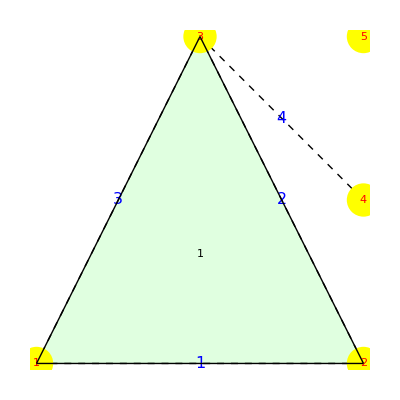

```mathematica
ShowTissue[q, "Vertices"-> {Yellow, PointSize[.06]}, "VertexNumbers"->{Red, FontSize-> 20}, "CellNumbers"-> True , "EdgeNumbers"-> True, "EdgeNumberStyle"-> {Blue,FontSize-> 16}, "All"-> True , "EdgeStyles"-> Dashed]
```

## Remove a specific dangling edge

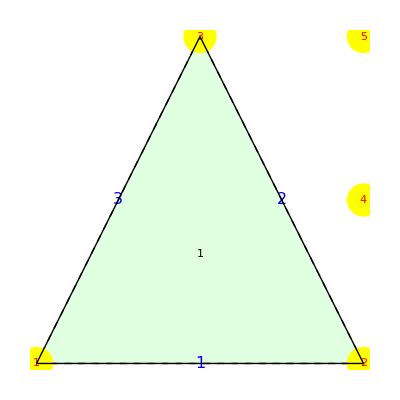

```mathematica
ShowTissue[UndangleEdge[q, 4],"Vertices"-> {Yellow, PointSize[.06]}, "VertexNumbers"->{Red, FontSize-> 20}, "CellNumbers"-> True , "EdgeNumbers"-> True, "EdgeNumberStyle"-> {Blue,FontSize-> 16}, "All"-> True , "EdgeStyles"-> Dashed]
```

## Removing Edge 4 followed by vertex 4 makes the old vertex 5 (still dangling) a new (still dangling) vertex 4

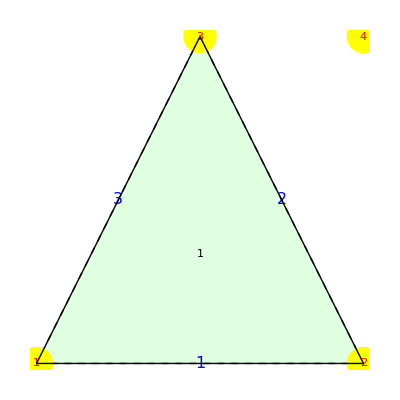

```mathematica
ShowTissue[UndangleVertex[UndangleEdge[q,4], 4],"Vertices"-> {Yellow, PointSize[.06]}, "VertexNumbers"->{Red, FontSize-> 20}, "CellNumbers"-> True , "EdgeNumbers"-> True, "EdgeNumberStyle"-> {Blue,FontSize-> 16}, "All"-> True , "EdgeStyles"-> Dashed]
```